Ans to the question 5 (a)

```mathematica
DSolve[y'[x]==((2y[x]+3)/(4x+5))^2,y[x],x]
```

{{y[x]→(-7-8 x-60 C[1]-48 x C[1])/(2 (-1+20 C[1]+16 x C[1]))}}

```mathematica
sol = y[x] /.%1 /.C[1] -> a
```

{(-7-60 a-8 x-48 a x)/(2 (-1+20 a+16 a x))}

```mathematica
Table[sol,{a,-2,2}]
```

{{(113+88 x)/(2 (-41-32 x))},{(53+40 x)/(2 (-21-16 x))},{1/2 (7+8 x)},{(-67-56 x)/(2 (19+16 x))},{(-127-104 x)/(2 (39+32 x))}}

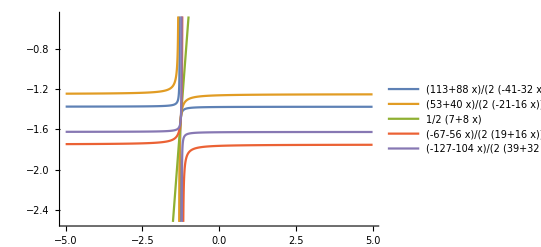

```mathematica
Plot[Evaluate[Table[sol,{a,-2,2}]],{x,-5,5},PlotLegends->"Expressions"]
```